New Bloody Mary
Modelování přenosu krevních plynů

```mathematica
Disociační křivka kyslíku
```

Disociační křivka kyslíku

```mathematica
(*
function - Oxygen dissociation curve 
  ODC[pO2_, pHp_, pCO2_, cDPG_, FCOHb_, FMetHb_, FHbF_, temp_]
 inputs : 	pO2    - tension of oxygen, [kPa]
		pHp    - plasma pH
		pCO2   - tension of carbon dioxide, [kPa]
		cDPG   - concentration of 2,3-DPG, [mmol/l]
		FCOHb  - fraction of carboxyhemoglobin
		FMetHb - fraction of 
		FHbF   - fraction of fetal hemoglobin
		temp   - actual temperature, [st C]
output :      s      - coefficient to compute saturation of oxygen
*)

ODC [pO2_,pHp_,pCO2_,cDPG_,FCOHb_,FMetHb_,FHbF_,temp_]:= 
Module[{a1,a10,a2,a20,a3,a30,a4,a40,a5,a50,a60,a6,ac,aa,temp0,b,p00,x00,x0,pO20,k0,s0,x,t,h0,h,y0,y,pH0,pCO20,cDPG0,s},
pH0 = 7.4;
a10 = -0.88; (*coefficient for pH displacement*)
a1=a10*(pHp-pH0);	(* -a10*(pHp-pH0) původn*)
(* pCO2 correction *)
pCO20 = 5.33;
a20 = 0.048;		(*coefficient for pCO2 displacement*)
	                                           (*! 0.048 disagreement with manual*)
a2 = a20 * Log[pCO2/pCO20];
(* FCOHb correction *)
a30 = -1.16;
a3 = a30 * FCOHb;
(*FMetHb correction*)
a40 = -0.7;
a4 = a40 * FMetHb;
(*FHbF correction*)
a50 = -0.25; 		(* coefficient for HbF displacement*)
a5 = a50 * FHbF;
(*cDPG correction*)
cDPG0 = 5;
a60 = 0.06 - 0.02 * FHbF;
a6 = a60 * (cDPG - cDPG0);
(*corrections summary*)
ac = a1+a2+a3+a4+a5;
(*
ac=-0.88*(pHp-7.4)+0.048*Log[pCO/5.33]-1.16*FCOHb-0.7*FMetHb-0.25*FHbF
+ (0.06-0.02*FHbF)*(cDPG-5)



a=-0.88*(pH-7.4)
+0.048*log(pCO2/5.33)
-0.7*FMetHb
+(0.3-0.25*FHbF)*cDPG/5-1;
*)
aa = ac + a6;
(* correction to the temperature*)
temp0 = 37;
b = 0.055 * (temp - temp0 ); 	
(*summary corrections to all displacements*)
p00 = 7.;	
x00 = Log [p00];	
x0 = x00 + aa + b;
pO20 = 7.0;
(*x  = log(pO2./pO20) - a;*)
If[(pO2==0),x=0,x  = Log[pO2]];
k0 = 0.5343;		
(*t = tanh(k_0 * (x))*) 
t = Tanh[k0 * (x-x0)]; 
h0 = 3.5;	
h = h0 + aa;		
s0 = 0.867;	(* saturation *)
y0 = Log[s0/(1-s0)];	
(*y  = y_0 + (x) + h*t*)
y  = y0 + (x-x0) + h*t;
(* finally compute the saturation*)
s = Exp[y]/(1+Exp[y])
(*end of ODC
refer to :
  1. Siggaard-Andersen O, Wimberley PD, Fogh-Andersen N, Gothgen IH.
     Measured and derived quantities with modern pH and blood gas equipment:
     calculation algorithms with 54 equations. 
     Scand J Clin Lab Invest 1988; 48, Suppl 189: 7-15.
  2. Siggaard-Andersen O, Siggaard-Andersen M. The oxygen status algorithm: 
     a computer program for calculating and displaying pH and blood gas data.
     Scand J Clin Lab Invest 1990; 50,  Suppl 203: 29-45.
*)
]
```

```mathematica
ODC [13.5,7.4,40,0.5,0.005,0.005,0.005,37]
```

0.983874

```mathematica
ODC[13.5,7.4,40,0.5,0.005,0.005,0.005,37]
```

0.983874

```mathematica
k=0.133322;
Manipulate[
Plot[ODC [pO2*k,pH,pCO2*k,5.0,0.005,0.005,0.005,temp],{pO2,0.0,120},PlotRange ->{0,1}],
{{pH,7.4},6.6,7.9},
{{pCO2,40},10,120},
{{temp,37},15,42}
]
```

```mathematica
ODC [13.3,7.410,40*0.133322,5.0,0.005,0.005,0.005,37]
```

0.976264

```mathematica
sO2of [5.5,7.21,6.13,0.5,0.005,0.005,0.005,37]
ODC[5.5,7.21,6.13,0.5,0.005,0.005,0.005,37]
```

0.816056

0.816886

```mathematica
pO2pCO2pHtemp= {
			{13.3,5.3,7.4,37},
			{5,5.3,7.4,37},
			{5,5.3,7.2,37},
			{5,5.3,7.8,37},
			{5,10,7.4,37},
			{5,2,7.4,37},
			{5,5.3,7.4,27},
			{5,5.3,7.4,47}
			};
Print ["sO2 při různých hodnotách pO2, pCO2, pH a teploty"]
Print ["(cDPG=0 mmol/l FCOHb=0 FMetHb=0.005 FHbF = 0.005):"]
For[i=1,i≤Length[pO2pCO2pHtemp],i++,
pO2=pO2pCO2pHtemp[[i]][[1]];
pCO2=pO2pCO2pHtemp[[i]][[2]];
pH=pO2pCO2pHtemp[[i]][[3]];
temp=pO2pCO2pHtemp[[i]][[4]];
sO2=ODC [pO2,pH,pCO2,5.4,0,0.005,0.005,temp];
Print["sO2="<>ToString[sO2*100]<>"% PO2="
<>ToString[pO2]<>"kPa PCO2="
<>ToString[pCO2]<>"kPa pH="
<>ToString[pH]<>" temp="
<>ToString[temp]<>"°C"
];
]
```

sO2 při různých hodnotách pO2, pCO2, pH a teploty

(cDPG=0 mmol/l FCOHb=0 FMetHb=0.005 FHbF = 0.005):

sO2=97.4103% PO2=13.3kPa PCO2=5.3kPa pH=7.4 temp=37°C

sO2=70.2444% PO2=5kPa PCO2=5.3kPa pH=7.4 temp=37°C

sO2=57.9684% PO2=5kPa PCO2=5.3kPa pH=7.2 temp=37°C

sO2=86.5937% PO2=5kPa PCO2=5.3kPa pH=7.8 temp=37°C

sO2=68.2912% PO2=5kPa PCO2=10kPa pH=7.4 temp=37°C

sO2=73.0788% PO2=5kPa PCO2=2kPa pH=7.4 temp=37°C

sO2=91.9371% PO2=5kPa PCO2=5.3kPa pH=7.4 temp=27°C

sO2=35.1693% PO2=5kPa PCO2=5.3kPa pH=7.4 temp=47°C

```mathematica
aFrom[pH_,pCO2_,MetHb_,HbF_,cDPG_] :=Module[
{
   dadpH=-0.88,
         dadlnpCO2=0.048,
         dadxMetHb=-0.7,
         dadxHbF=-0.25,
 
 dadcDPG0=0.3,
  pH0=7.40,
  pCO20=5.33,
  dadcDPGxHbF=-0.1,
  cDPG0=5.0
},
dadpH*(pH-pH0)
    +dadlnpCO2*Log[(pCO2/pCO20)]
   +dadxMetHb*MetHb
   +dadxHbF*HbF
    +(dadcDPG0+dadcDPGxHbF*HbF)*(cDPG/cDPG0-1.0)
]

sCO[FCOHb_,FMetHb_]:=Module[{xFCOHb},
If[FCOHb<0,xFCOHb=0,xFCOHb=FCOHb];
xFCOHb/(1.0-FMetHb)
]

  antilogit[x_]:=Exp[x]/(1.0+Exp[x])

logit[x_]:= Log[x/(1-x)]

h[a_]:=Module[
{h0=3.5},
h0+a
]

x[pO2CO_,a_,T_] := Module[
{p0=7.0,
T0=37.0,
dbdT=0.055(*/K;used by pO2fr(),pO2of()*)
},
Log[pO2CO/p0]-a-dbdT*(T-T0)
]


dydx[pO2CO_,a_,T_]:=Module[
{k=0.5342857},
1+h[a]*k*(1-(Tanh[k*x[pO2CO,a,T]])^2)
]

 y[pO2CO_,a_,T_] :=Module[
{y0=1.8747,
k=0.5342857},
 y0+x[pO2CO,a,T]+h
[a]*Tanh[k*x[pO2CO,a,T]] 
]

sO2CO[pO2CO_,a_,T_]:=antilogit[y[pO2CO,a,T]]

MpCOof[pO2CO_,a_,T_,FCOHb_,FMetHb_]:=(pO2CO/sO2CO[pO2CO,a,T])*sCO[FCOHb,FMetHb]                                                                                              

pO2fr[sO2_,a_,T_,FCOHb_,FMetHb_]:=Module[
{pO2CO,sO2CO,ym,yc,dydxc,p0=7.0,dbdT=0.055,T0=37,doit,Epsilon=0.000001},
pO2CO=Exp[Log[p0]+a+dbdT*(T-T0)];
      sO2CO=sO2+sCO[FCOHb,FMetHb]*(1-sO2);
      ym=logit[sO2CO];
doit=False;
While[!doit,
yc=y[pO2CO,a,T];
dydxc=dydx[pO2CO,a,T];
pO2CO=Exp[Log[pO2CO]+(ym-yc)/dydxc];
doit = Abs[ym-yc]<Epsilon;
];
pO2CO-MpCOof[pO2CO,a,T,FCOHb,FMetHb]
];

sO2fr[pO2CO_,a_,T_,FCOHb_,FMetHb_]:=Module[
{sO2COc,sCOc},
sO2COc=sO2CO[pO2CO,a,T];
sCOc=sCO[FCOHb,FMetHb];
(sO2COc-sCOc)/(1-sCOc)
]

sO2of [pO2T_,pHT_,pCO2T_,cDPG_,FCOHb_,FMetHb_,FHbF_,TPt_]:=Module[
{MpCOa,MpCOb,sCOc,doit,a,Epsilon=0.000001},
a= aFrom[pHT,pCO2T,FMetHb,FHbF,cDPG];
sCOc:=sCO[FCOHb,FMetHb];
If [sCOc>0 , MpCOa=pO2fr[sCOc,a,TPt,0,FMetHb], MpCOa:=0];
      MpCOb=MpCOa;
doit =False;
 While[!doit,
MpCOb=0.6*MpCOa+0.4*MpCOb;
MpCOa=MpCOof[pO2T+MpCOb,a,TPt,FCOHb,FMetHb];
doit=(Abs[MpCOa-MpCOb]<Epsilon);
];
 sO2fr[pO2T+MpCOa,a,TPt,FCOHb,FMetHb]
];
```

```mathematica
sO2of [13.5,7.4,5.4,0.5,0.005,0.005,0.005,37]
```

0.986557

todo :

O2total
CO2total
PO2PCO2
O2CO2
ALV
CIRKULACE
Wagneriáda

```mathematica
aO2[temp_] := Exp[Log[0.0105]+-0.0115*(temp-37.0)+0.5*0.00042*(temp-37.0) ^2];
ceHbof[ctHb_,FCOHb_,FMetHb_]:=ctHb*(1-FCOHb-FMetHb);
dissO2[pO2_,temp_]:= aO2[temp]*pO2;
ctO2of[pO2_,sO2_, ctHb_,FCOHb_,FMetHb_,temp_]:=dissO2[pO2,temp]+sO2*ceHbof[ctHb,FCOHb,FMetHb];
```

```mathematica
aO2[38]
```

0.0103821

```mathematica
ceHbof[9.2,0.005,0.005]
```

9.108

```mathematica
ODC[5,7.410,5.14,5.4,0.005,0.005,0.005,37]
sO2of[5,7.410,5.14,5.4,0.005,0.005,0.005,37]
```

0.71241

0.711486

```mathematica
aO2[37]
dissO2[0,37]
```

0.0105

0.

```mathematica
O2totalold[ctHb_,pO2_,pHp_,pCO2_,cDPG_,FCOHb_,FMetHb_,FHbF_,temp_] :=Module[
{cef,ctO2,sO2,sO2new,ctO2new},
sO2=ODC [pO2,pHp,pCO2,cDPG,FCOHb,FMetHb,FHbF,temp];
cef=ceHbof[ctHb,FCOHb,FMetHb];
ctO2 = ctO2of[pO2,sO2, ctHb,FCOHb,FMetHb,temp]
]

O2total[ctHb_,pO2_,pHp_,pCO2_,cDPG_,FCOHb_,FMetHb_,FHbF_,temp_] :=Module[
{cef,ctO2,sO2,sO2new,ctO2new},
sO2=sO2of [pO2,pHp,pCO2,cDPG,FCOHb,FMetHb,FHbF,temp];
cef=ceHbof[ctHb,FCOHb,FMetHb];
ctO2 = ctO2of[pO2,sO2, ctHb,FCOHb,FMetHb,temp]
]
```

```mathematica
sO2of[5,7.410,5.14,5,0.005,0.005,0.005,37]
```

0.725893

```mathematica
O2totalold[9,5,7.410,5.14,5,0.005,0.005,0.005,27]
O2total       [9,5,7.410,5.14,5,0.005,0.005,0.005,27]
```

8.32071

8.31725

```mathematica
k=0.133322;
Manipulate[
Plot[{sO2of [pO2*k,pH,pCO2*k,5.0,0.005,0.005,0.005,temp],ODC [pO2*k,pH,pCO2*k,5.0,0.005,0.005,0.005,temp]},{pO2,0,120},PlotRange ->{0,1}],
{{pH,7.4},6.6,7.9},
{{pCO2,40},10,120},
{{temp,37},15,42}

]
```

```mathematica
k=0.133322;
Manipulate[
Plot[{sO2of [pO2*k,pH,pCO2*k,5.0,0.005,0.005,0.005,temp]-ODC [pO2*k,pH,pCO2*k,5.0,0.005,0.005,0.005,temp]},{pO2,0,120},PlotRange ->{0,0.01}],
{{pH,7.4},6.6,7.9},
{{pCO2,40},10,120},
{{temp,37},15,42}

]
```

```mathematica
k=0.133322;
Manipulate[
Plot[{O2total [ctHb, pO2*k,pH,pCO2*k,cDPG,0.005,0.005,0.005,temp],O2totalold [cHb/1.6114, pO2*k,pH,pCO2*k,cDPG,0.005,0.005,0.005,temp],dissO2[pO2*k,temp]},{pO2,0.0,350},PlotRange ->{0,15}],
{{pH,7.4},6.6,7.9},
{{pCO2,40},10,120},
{{temp,37},15,42},
{{cHb, 15},8,28},
{{cDPG,5},3,8}

]
```

Disociační křivka oxidu uhličitého

    pHTpCO2T:      begin
      //pCO2m    :=pCO22of (pCO2T, TPt,      Tm,   ctHb);
      pCO2m := pCO22of(pCO2T, TPt, Tm, ctHb, cAlb, pHT);
      //pHm      :=pH2of   (pHT,   TPt,  Tm,    ctHb);
      pHm := pH2of (pHT, TPt, Tm, ctHb, cAlb, pCO2T);
      cBaseEcf :=cBaseof (pHm,   pCO2m,    ctHb*FBEcf, Tm);
      ctCO2PT  :=ctCO2Pof(pHT,   pCO2T,    TPt)
                   end;
                   
  Function antilg(x: Double):   Double;   begin result:= exp(ln(10)*x)     end;
  Function lg(x:Double):        Double;   begin result:= (ln(x))/ln(10)    end;
  
   
   
  {for cHCO3of(), pCO2of(), pCO2af(), pH2of(), pCO22of(), pHfr()}
FUNCTION aCO2of(T: Double): Double;
  Const  aCO2T0 = 0.23 {mM/kPa}; dlgaCO2dT = -0.0092 {lg(mM/kPa)/K};
  Begin  Result:= aCO2T0 * antilg(dlgaCO2dT*(T - T0)) End;

{used for calculation of ctCO2P}
FUNCTION ctCO2Pof(pH, pCO2, T: Double): Double;
  Begin  Result:= pCO2*aCO2of(T)*(1+antilg(pH - pKof(T)))     End;
  
  {for cHCO3of(), pCO2of(), pCO2af(), pH2of(), pCO22of(), pHfr()}
FUNCTION aCO2of(T: Double): Double;
  Const  aCO2T0 = 0.23 {mM/kPa}; dlgaCO2dT = -0.0092 {lg(mM/kPa)/K};
  Begin  Result:= aCO2T0 * antilg(dlgaCO2dT*(T - T0)) End;
  
  

  
  {for cHCO3of(), pCO2of(), pCO2af(), pHfr()}
FUNCTION pKof(T: Double): Double;
  Const  pKT0   = 6.1; dpKdT  = -0.0026;
  Begin  Result:= pKT0 + dpKdT*(T - T0) {-lg(1+antilg(pH-8.7))} End;
  
  
  {used by pH2of(), pCO22of(), cBaseof(), pCO2fr(), calculation of cHCO3}
FUNCTION cHCO3of(pH, pCO2, T: Double): Double;
  Begin  Result:= pCO2*aCO2of(T)*antilg(pH - pKof(T))  End;
  
  {used by cBaseof() and calculation of pCO2T or pCO2m}
  function pCO22of(pCO21, T1, T2, cHb, cAlb, pH1: Double): Double;
//Eqn. 10 and 11, p. 87 i min bog.
var betaX, dpHdT1, pH2, cHCO3, dlgpCO2dT1, pCO22, dpHdT2, dlgpCO2dT2,
      dpHdTmean, dlgpCO2dTMean: Double;
  begin
    betaX:= 7.7+8*(cAlb-cAlbN) + 2.3*cHb;

    dpHdT1:= (-0.0026 -
      betaX*0.016*(1/(2.3*cHCO3of(pH1,pCO21,T1)) + 1/(2.3*pCO21*aCO2of(T1))))/
      (1 + betaX* (1/(2.3*cHCO3of(pH1,pCO21,T1)) + 1/(2.3*pCO21*aCO2of(T1))));
    pH2:= pH1 + dpHdT1*(T2-T1);

    cHCO3:= cHCO3of(pH1,pCO21,T1);
    dlgpCO2dT1:= -0.0026 - (-0.0092) - dpHdT1 +
      (1/(2.3*cHCO3))* (betax*dpHdT1 + betax*0.016);
    pCO22:= antilg(lg(pCO21) + dlgpCO2dT1*(T2-T1));

    dpHdT2:= (-0.0026 -
      betaX*0.016*(1/(2.3*cHCO3of(pH2,pCO22,T2)) + 1/(2.3*pCO22*aCO2of(T2))))/
      (1 + betaX* (1/(2.3*cHCO3of(pH2,pCO22,T2)) + 1/(2.3*pCO22*aCO2of(T2))));
    dpHdTmean:= (dpHdT1 + dpHdT2)/2;
    pH2:= pH1 + dpHdTmean*(T2-T1);

    cHCO3:= cHCO3of(pH2,pCO22,T2);
    dlgpCO2dT2:= -0.0026 - (-0.0092) - dpHdT2 +
      (1/(2.3*cHCO3))* (betax*dpHdT2 + betax*0.016);
    dlgpCO2dTmean:= (dlgpCO2dT1 + dlgpCO2dT2)/2;

    Result:= antilg(lg(pCO21) + dlgpCO2dTmean*(T2-T1));
  end;

function pH2of(pH1, T1, T2, cHb, cAlb, pCO21: Double): Double;
//Eqn. 10 and 11, p. 87 i min bog.
var betaX, dpHdT1, pH2, cHCO3, dlgpCO2dT1, pCO22, dpHdT2,
      dpHdTmean: Double;
  begin
     betaX:= 7.7+8*(cAlb-cAlbN) + 2.3*cHb;

    dpHdT1:= (-0.0026 -
      betaX*0.016*(1/(2.3*cHCO3of(pH1,pCO21,T1)) + 1/(2.3*pCO21*aCO2of(T1))))/
      (1 + betaX* (1/(2.3*cHCO3of(pH1,pCO21,T1)) + 1/(2.3*pCO21*aCO2of(T1))));
    pH2:= pH1 + dpHdT1*(T2-T1);

    cHCO3:= cHCO3of(pH1,pCO21,T1);
    dlgpCO2dT1:= -0.0026 - (-0.0092) - dpHdT1 +
      (1/(2.3*cHCO3))* (betax*dpHdT1 + betax*0.016);
    pCO22:= antilg(lg(pCO21) + dlgpCO2dT1*(T2-T1));

    dpHdT2:= (-0.0026 -
      betaX*0.016*(1/(2.3*cHCO3of(pH2,pCO22,T2)) + 1/(2.3*pCO22*aCO2of(T2))))/
      (1 + betaX* (1/(2.3*cHCO3of(pH2,pCO22,T2)) + 1/(2.3*pCO22*aCO2of(T2))));
    dpHdTmean:= (dpHdT1 + dpHdT2)/2;
    Result:= pH1 + dpHdTmean*(T2-T1);
  end;

  
  
  {New function: used for calculation of RQ}
FUNCTION ctCO2Bof(pH, pCO2, T, ctHb, sO2: Double): Double;
  Const dpHEdpHP = 0.77; dpHEdsO2 = 0.035; pHEx= 7.84; sO2x = 0.06;
          aCO2E0 = 0.195; ctHbE = 21; pHE0 = 7.19; pKE0 = 6.125;
  Var pHT0, pCO2T0, pKE, pHE, ctCO2E, ctCO2B, phiEB:  Double;
  Begin
   // pCO2T0 := pCO22of   (pCO2, T, T0, ctHb);
    pCO2T0 := pCO22of(pCO2, T, T0, ctHb, cAlb, pH);
 //   pHT0   := pH2of (pH, T, T0, ctHb);
    pHT0 := pH2of (pH, T, T0, ctHb, cAlb, pCO2);
    pHE:= pHE0 + dpHEdpHP*(pHT0 - pH0) + dpHEdsO2*(1 - sO2);
      {or: (pHE - 6.9) = alpha * (pHP - pH0), where alpha = 0.7 + f*(1-sO2)}
    pKE:= pKE0 - lg(1 + antilg(pHE - pHEx - sO2x*sO2));
    ctCO2E:= aCO2E0*pCO2T0*(1 + antilg(pHE - pKE));
    phiEB:= ctHb/ctHbE;  //!!!! to je hematokrit!!!!!!!
    ctCO2B:= ctCO2E*phiEB + ctCO2Pof(pHT0,pCO2T0,T0)*(1-phiEB);
    Result:= ctCO2B
  End;

```mathematica
antilg[x_]:= Exp[Log[10]*x] 

 lg[x_] :=Log[x]/Log[10]

aCO2of[T_] :=Module[
{aCO2T0=0.23 , dlgaCO2dT=-0.0092 , T0=37.0}, 
      aCO2T0* antilg[dlgaCO2dT*(T-T0)] 
]

pKof[T_] := Module[{pKT0=6.1,dpKdT=-0.0026, T0=37.0},
pKT0+dpKdT*(T-T0)
]

ctCO2Pof[pH_,pCO2_,T_]:=pCO2*aCO2of[T]*(1+antilg[pH-pKof[T]])


cHCO3of[pH_,pCO2_,T_] :=pCO2*aCO2of[T]*antilg[pH-pKof[T]];

pCO22of [pCO21_,T1_,T2_,cHb_,cAlb_,pH1_] := Module[
{ betaX,dpHdT1,pH2,cHCO3,dlgpCO2dT1,pCO22,dpHdT2,dlgpCO2dT2,dpHdTmean,dlgpCO2dTmean, cAlbN},
      cAlbN=0.66;
betaX=7.7+8*(cAlb-cAlbN)+2.3*cHb;
dpHdT1=(-0.0026-betaX*0.016*(1/(2.3*cHCO3of [pH1,pCO21,T1])+1/(2.3*pCO21*aCO2of[T1])))/(1+betaX*(1/(2.3*cHCO3of[pH1,pCO21,T1])+1/(2.3*pCO21*aCO2of[T1])));
pH2=pH1+dpHdT1*(T2-T1);
cHCO3=cHCO3of[pH1,pCO21,T1];
dlgpCO2dT1=-0.0026-(-0.0092)-dpHdT1+(1/(2.3*cHCO3))*(betaX*dpHdT1+betaX*0.016);pCO22= antilg[lg[pCO21]+dlgpCO2dT1*(T2-T1)];
dpHdT2=(-0.0026-betaX*0.016*(1/(2.3*cHCO3of[pH2,pCO22,T2])+1/(2.3*pCO22*aCO2of[T2])))/(1+betaX*(1/(2.3*cHCO3of[pH2,pCO22,T2])+1/(2.3*pCO22*aCO2of[T2])));dpHdTmean=(dpHdT1+dpHdT2)/2;pH2=pH1+dpHdTmean*(T2-T1);
cHCO3=cHCO3of[pH2,pCO22,T2];
dlgpCO2dT2=-0.0026-(-0.0092)-dpHdT2+(1/(2.3*cHCO3))*(betaX*dpHdT2+betaX*0.016);dlgpCO2dTmean=(dlgpCO2dT1+dlgpCO2dT2)/2;
antilg[lg[pCO21]+dlgpCO2dTmean*(T2-T1)]
]


pH2of[pH1_,T1_,T2_,cHb_,cAlb_,pCO21_]:=Module [{betaX,dpHdT1,pH2,cHCO3,dlgpCO2dT1,pCO22,dpHdT2,dpHdTmean,cAlbN=0.66},   betaX=7.7+8*(cAlb-cAlbN)+2.3*cHb;
dpHdT1=(-0.0026-betaX*0.016*(1/(2.3*cHCO3of[pH1,pCO21,T1])+1/(2.3*pCO21*aCO2of[T1])))/(1+betaX*(1/(2.3*cHCO3of[pH1,pCO21,T1])+1/(2.3*pCO21*aCO2of[T1])));
pH2=pH1+dpHdT1*(T2-T1);
cHCO3=cHCO3of[pH1,pCO21,T1];
dlgpCO2dT1=-0.0026-(-0.0092)-dpHdT1+(1/(2.3*cHCO3))*(betaX*dpHdT1+betaX*0.016);pCO22=antilg[lg[pCO21]+dlgpCO2dT1*(T2-T1)];
dpHdT2=(-0.0026-betaX*0.016*(1/(2.3*cHCO3of[pH2,pCO22,T2])+1/(2.3*pCO22*aCO2of[T2])))/(1+betaX*(1/(2.3*cHCO3of[pH2,pCO22,T2])+1/(2.3*pCO22*aCO2of[T2])));dpHdTmean=(dpHdT1+dpHdT2)/2;pH1+dpHdTmean*(T2-T1)
]



ctCO2Bof[pH_,pCO2_,T_,ctHb_,sO2_]:= Module [{dpHEdpHP=0.77,dpHEdsO2=0.035,pHEx=7.84,sO2x=0.06,
aCO2E0=0.195,ctHbE=21,pHE0=7.19,pKE0=6.125,cAlbN=0.66, T0=37,pH0=7.4,
pHT0,pCO2T0,pKE,pHE,ctCO2E,ctCO2B,phiEB, cAlb},
cAlb=cAlbN;
          (*albumin has minimal influence on total CO2 concentration*);
                (*pCO2T0:=pCO22of (pCO2,T,T0,ctHb)*);
pCO2T0=pCO22of[pCO2,T,T0,ctHb,cAlb,pH];
                  (*pHT0:=pH2of (pH,T,T0,ctHb)*);
pHT0=pH2of [pH,T,T0,ctHb,cAlb,pCO2];
pHE=pHE0+dpHEdpHP*(pHT0-pH0)+dpHEdsO2*(1-sO2);
                (*or:(pHE-6.9)=alpha*(pHP-pH0),where alpha=0.7+f*(1-sO2)*);
pKE=pKE0-lg[1+antilg[pHE-pHEx-sO2x*sO2]];
ctCO2E=aCO2E0*pCO2T0*(1+antilg[pHE-pKE]);
phiEB=ctHb/ctHbE;(*!!!!it is hematocrit!!!!!!!*) 
ctCO2B=ctCO2E*phiEB+ctCO2Pof[pHT0,pCO2T0,T0]*(1-phiEB)
]
```

```mathematica
ctCO2Bof[7.410,2.57,37,9,0.976]
```

10.5006

```mathematica
ctCO2Bof[7.000,5.33,37,8,0.942]
```

9.67713

21.0013

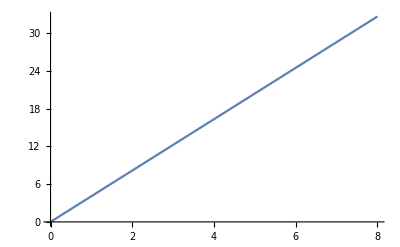

```mathematica
21.00125209326405
Plot[ctCO2Bof[7.410,pCO2,37,9,0.978], {pCO2, 0,8}]
```

```mathematica
Manipulate[
Plot[ctCO2Bof [pH,pCO2,temp,cHb,sO2*0.01],{pCO2,0.0,8},PlotRange ->{0,30}],
{{pH,7.4},6.6,7.9},
{{sO2,97},20,99.99},
{{temp,37},15,42},
{{cHb, 9},5,16}

]
```

```mathematica
Van Slyke equation
```

equation Slyke Van

{....... Van Slyke equation:   ................................................}
CONST  betaP= 7.7; betaHb= 2.3;  ctHbb= 43.0;

{used by pCO2fr(), pHfr(), and Calculation x 1}
{pH and pCO2 are referred to 37 řC;
 alternatively pH0 and pCO20 (i.e. the titration endpoint)
 could be converted to T; the result ought to be the same}
FUNCTION  cBaseOf(pH, pCO2, cHb, T: Double): Double;
  Var pHT0, pCO2T0: Double;
  Begin
    cAlbN:=0.66;
    //pCO2T0 := pCO22of(pCO2, T, T0, ctHb);
    pCO2T0 := pCO22of(pCO2, T, T0, cHb, cAlb, pH);
    //pHT0   := pH2of(pH, T, T0, ctHb);
    pHT0 := pH2of(pH, T, T0, ctHb, cAlb, pCO2);
    Result := (1-cHb/ctHbb)
                 *(cHCO3of(pHT0,pCO2T0,T0) - cHCO3of(pH0, pCO20, T0)
                     + (betaHb*cHb + betaP+8*(cAlb-cAlbN))*(pHT0-pH0))
  End; {cBaseOf}

{used by pCO2fr() and Calculation to check for negative value}
function cHCO3fr(pH, cBase, cHb, T: Double): Double;
  var pHT0: Double;
  begin
    cAlbN:=0.66;
    //pHT0:= pH2of(pH, T, T0, cHb);
    pHT0:= pH2of(pH, T, T0, cHb, cAlb, pCO2T);
    Result := cBase/(1-cHb/ctHbb)  + cHCO3of(pH0, pCO20, T0)
                     - (betaHb*cHb + betaP+8*(cAlb-cAlbN))*(pHT0 - pH0)
  end; {cHCO3fr()} {Can be negative!!!}
  
{used once by Calculation}
function pCO2fr(pH, cBase, cHb, T: Double): Double;
  var cHCO3: Double;
  begin cHCO3:=cHCO3fr(pH, cBase, cHb, T);
  if cHCO3>0 then Result:=pCO2of(pH, cHCO3, T) else Result:=-1
  end; {pCO2fr}
  
function  pHfr(pCO2, cBase, cHb, T: Double): Double;//Conversion to 37 C, calculation, conversion to T
  var pCO237, pH37guess, cBaseGuess: Double;
  begin
    pH37guess:= pH0; cAlbN:=0.66;
    //pCO237:=pCO22of(pCO2, T, T0, cHb);
    pCO237:= pCO22of(pCO2, T, T0, cHb, cAlb, pH37Guess);
    cBaseGuess:=cBaseof(pH37guess, pCO237, cHb, T0);
    {Newton Raphson: We know cBase as a function of pH at constant pCO2,
      but cannot express pH as a function of cBase}
    repeat pH37Guess:=pH37Guess + (cBase - cBaseGuess)/((1-cHb/ctHbb)*
             (betaP+8*(cAlb-cAlbN) + betaHb*cHb) + ln(10)*cHCO3of(pH37Guess, pCO237, T0));
           cBaseGuess:=cBaseof(pH37guess, pCO237, cHb, T0);
    until Abs(cBase - cBaseGuess) < epsilon;
    //Result:= pH2of(pH37guess, T0, T, cHb);
    Result:=pH2of(pH37guess, T0, T, cHb, cAlb, pCO237);
  end; {pHfr}

```mathematica
(*"Van Slyke equation"*)
cBaseOf   [ pH_,pCO2_, cHb_,  T_,cAlb_] := Module[{cAlbN=0.66,T0=37.0,ctHbb=43.0,
betaHb=2.3, betaP=7.7, pH0=7.40,pCO20=5.33,pHT0, pCO2T0,resultcBEox},
pCO2T0=pCO22of[pCO2,T,T0,cHb,cAlb,pH];
pHT0=pH2of[pH,T,T0,cHb,cAlb,pCO2];
result_cBEox = (1-cHb/ctHbb)
               *(cHCO3of[pHT0,pCO2T0,T0]-cHCO3of[pH0,pCO20,T0]+(betaHb*cHb+betaP+8*(cAlb-cAlbN))*(pHT0-pH0))

]



(* Conversion to 37 C, calculation pH, conversion to T *)
pHfr [pCO2_, cBEox_,cHb_,T_,cAlb_]:=
Module[{pCO237,pH37Guess=7.4,cBEoxGuess, pH0=7.4,T0=37,cAlbN=0.66,betaHb=7.7, betaP=2.3,ctHbb=43.0,doit, epsilon=0.000001,resultpH},
pCO237=pCO22of[pCO2,T,T0,cHb,cAlb,pH37Guess];cBEoxGuess=cBaseOf[pH37Guess,pCO237,cHb,T0,cAlb];

doit = False;
While[! doit,
pH37Guess=pH37Guess+(cBEox-cBEoxGuess)/((1-cHb/ctHbb)*(betaP+8*(cAlb-cAlbN)+betaHb*cHb)+Log[10.0]*cHCO3of[pH37Guess,pCO237,T0]);
cBEoxGuess=cBaseOf[pH37Guess,pCO237,cHb,T0,cAlb];
doit=Abs[cBEox-cBEoxGuess]<epsilon;
]  ;
resultpH = pH2of[pH37Guess,T0,T,cHb,cAlb,pCO237]
]
```

```mathematica
cBaseOf[ 7.0,5.33, 8.0*0.33, 27,0.66]
```

-18.8564

pHfr [5.3, -0.112,8,37,0.66]

```mathematica
pHfr [5.33,-18.8564,8*0.33,27,0.66]
```

7.00684

```mathematica
ctCO2Bof[7.037,5.33,37,8,0.946]
ctCO2Bof[7.000,5.33,37,8,0.942]
```

10.3972

9.67713

```mathematica
cCO2total [cB_, pCO2_,temp_,cHb_,sO2_ ]:=Module[{pH},
pH=pHfr [pCO2, cB,cHb,temp,0.66];
ctCO2Bof [pH,pCO2,temp,cHb,sO2]
 ]

cCO2total[0,5.3,37,8,1]

Manipulate[
Plot[cCO2total[0,pCO2,temp,cHb,sO2*0.01],{pCO2,0.0,8},PlotRange ->{0,30}],
{{sO2,97},20,99.99},
{{temp,37},15,42},
{{cHb, 9},5,16}
]
```

21.7465

```mathematica
cCO2total[0,5.3,37,8,1]
```

21.7465

```mathematica
c1=cCO2total[0,20*0.133322,37,8.4,1]

c2=cCO2total[0,80*0.133322,37,8.4,1]
dc=c2-c1
k=dc/60.0
k*22.25
c40=cCO2total[0,40*0.133322,37,8.4,1]
c48=cCO2total[0,48*0.133322,37,8.4,1]
P48x=(c48-c40)/0.19
```

16.4425

27.9382

11.4958

0.191596

4.26302

21.6018

23.1359

8.07423